```mathematica
primeTurn[n_Integer,dot_:10^5] :=Module[{q=1,
p=NextPrime[1],
step={1,0},
rotate=RotationMatrix[-π/2],
points={0,0}~Table~If[n>dot,PrimePi[n],n]},
If[n>dot,
Do[points[[i]]=points[[i-1]]+q step;
q=NextPrime[p]-p;p+=q;step=rotate.step,
{i,2,Length@points}],
Do[points[[i]]=points[[i-1]]+step;
If[i==p,p=NextPrime[p];step=rotate.step],
{i,2,n}]];
q=Max[If[n>dot,{8.33,.505},{4.24,.377}].{1,-Log[n]},.4];
p=If[n>dot,AbsolutePointSize@q,AbsoluteThickness@q];
Graphics[{p,Blue,If[n>dot,Point[#],Line[#]]&@points},
PlotRange->CoordinateBounds[points,1],ImageSize->Large]]
```

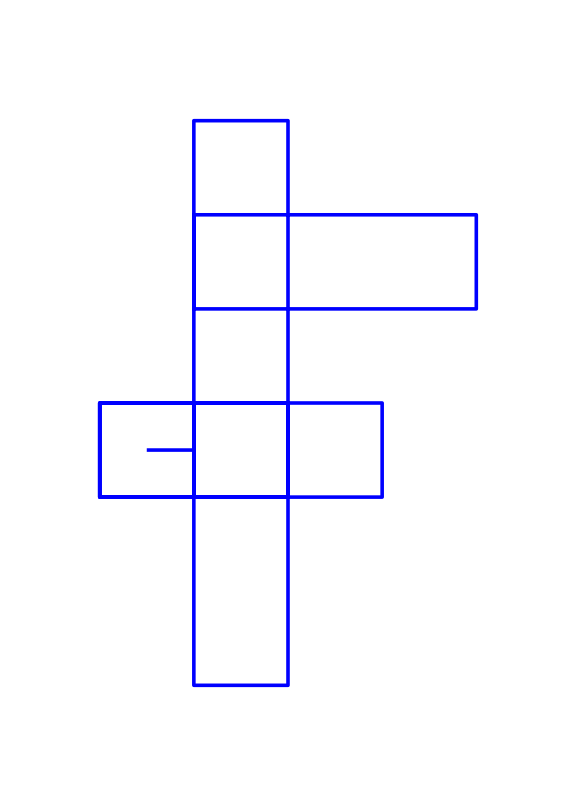

```mathematica
primeTurn[80]
```

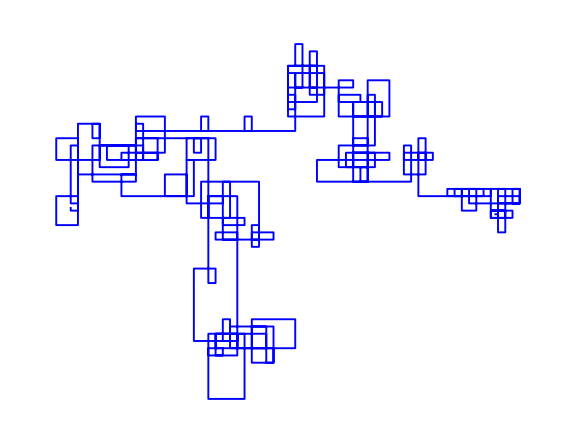

```mathematica
primeTurn[2000]
```

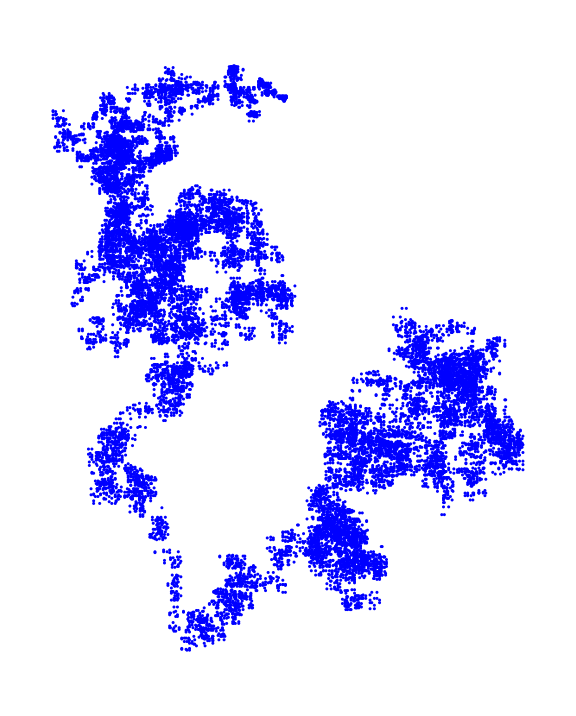

```mathematica
primeTurn[200000]
```